```mathematica
ing1[0.3,-1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.007697771786 ⅈ

```mathematica
NIntegrate[ng1[0.435,-1],{k3,0,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.003449987199 ⅈ

```mathematica
0.07
```

```mathematica
ing1[0.07,-1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.3918001995 ⅈ

```mathematica
NIntegrate[ng1[0.07,-1],{k3,0,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.0002097145066 ⅈ

```mathematica
intg2[y_]:=NIntegrate[ng1[y,-1],{k3,0,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}];
```

```mathematica
lg2=ParallelTable[{y,intg2[y]},{y,0,1.1,0.05}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
sg2=Interpolation[lg2];
```

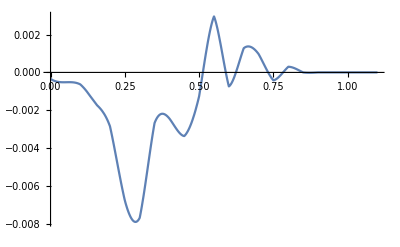

```mathematica
Plot[I*sg2[x],{x,0,1.1}]
```

```mathematica
sg2[0.28]
```

0.+0.0078786 ⅈ

```mathematica
NIntegrate[ng1[0.3,-1],{k3,0,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.007697770249 ⅈ

```mathematica
lg3=ParallelTable[{y,I*intg2[y]},{y,0,1.1,0.05}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

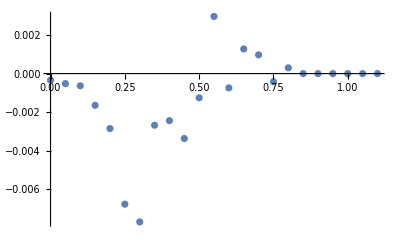

```mathematica
ListPlot[lg3]
```

```mathematica
lg3
```

{{0.,-0.0003389750318},{0.05,-0.0005200686039},{0.1,-0.0006328197327},{0.15,-0.001645878204},{0.2,-0.002853065072},{0.25,-0.006778960859},{0.3,-0.007697770249},{0.35,-0.002679726776},{0.4,-0.002442605535},{0.45,-0.003369197373},{0.5,-0.001255916326},{0.55,0.002966053442},{0.6,-0.0007407288817},{0.65,0.001279738085},{0.7,0.0009739054965},{0.75,-0.0004216918032},{0.8,0.000299802378},{0.85,1.299367202×10^-14},{0.9,2.116937538×10^-14},{0.95,1.348202004×10^-14},{1.,1.948462567×10^-14},{1.05,-4.755417801×10^-16},{1.1,-6.933156556×10^-15}}

```mathematica
NIntegrate[ng1[0.3,-1],{k3,0,10},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}]+NIntegrate[ng1[0.3,-1],{k3,10,50},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}]+NIntegrate[ng1[0.3,-1],{k3,50,200},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}]+NIntegrate[ng1[0.3,-1],{k3,200,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.08356711384892786845668071299407945298941848671964413455685×10^-6 ⅈ and 0.000211263985819264133604021096581830225601979095836567867958513 for the integral and error estimates.

2.06210388×10^-6 ⅈ

```mathematica
NIntegrate[ng1[0.3,-1],{k3,0,10},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.08356711384892786845668071299407945298941848671964413455685×10^-6 ⅈ and 0.000211263985819264133604021096581830225601979095836567867958513 for the integral and error estimates.

2.083567114×10^-6 ⅈ

```mathematica
NIntegrate[ng1[0.3,-1],{k3,10,50},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}]+NIntegrate[ng1[0.3,-1],{k3,50,200},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}]+NIntegrate[ng1[0.3,-1],{k3,200,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}]
```

-2.146323852×10^-8 ⅈ

```mathematica
NIntegrate[ng1[0.3,-1],{k3,0,10},{θ,0,π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.31320166123773993838803701437550374443508832299791313943498×10^-8 ⅈ and 1.76852083966237548388274665599047948295823208890256095638915×10^-7 for the integral and error estimates.

1.313201661×10^-8 ⅈ

```mathematica
NIntegrate[ng1[0.2,-1],{k3,10,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}]
```

-2.285620904×10^-8 ⅈ

```mathematica
NIntegrate[ng1[0.8,-1],{k3,0,10},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.95325238128443390323300036216787154802507862414527890505567×10^-9 ⅈ and 3.73693929662781313159190890601205858994623556767611562760306×10^-7 for the integral and error estimates.

3.953252381×10^-9 ⅈ

```mathematica
NIntegrate[ng1[y,-1],{y,0,1.1},{k3,10,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}]
```

-1.031310342×10^-8 ⅈ